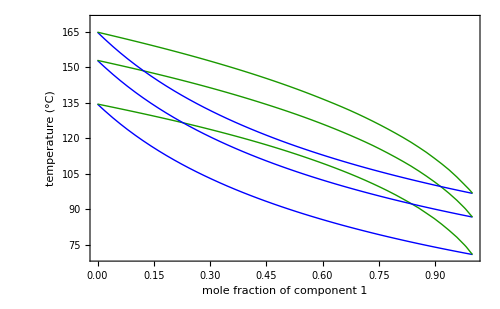

```mathematica
Module[{Tx1,Ty1,Tx15,Ty15,Tx2,Ty2,cs,p1,p2,p3},
Tx1=Interpolation[{{0.,134.48},{0.05,127.46001},{0.1,121.36},{0.15,115.99001},{0.2,111.21001},{0.25,106.92},{0.3,103.05},{0.35000003,99.51},{0.4,96.28},{0.45,93.3},{0.5,90.54},{0.55,87.97},{0.6,85.58},{0.65,83.33},{0.7000001,81.23},{0.75,79.24},{0.8,77.37},{0.85,75.59},{0.9,73.91},{0.9500001,72.31},{1.,70.78}}];
Ty1=Interpolation[{{0.,134.484},{0.20400001,127.461},{0.358,121.358},{0.47600003,115.988},{0.5680001,111.211},{0.642,106.925},{0.7020001,103.047},{0.751,99.514},{0.792,96.278},{0.8260001,93.296},{0.856,90.536},{0.88,87.97},{0.902,85.57601},{0.92,83.334},{0.936,81.227},{0.9510001,79.243},{0.963,77.369},{0.974,75.59401},{0.984,73.91},{0.992,72.309},{1.,70.783}}];

Tx15=Interpolation[{{0.05,145.8451},{0.1,139.5855},{0.15,134.0549},{0.2,129.118},{0.25,124.6721},{0.3,120.6381001},{0.35003,116.9536001},{0.4,113.569},{0.45,110.4438001},{0.5,107.5451},{0.55,104.8454},{0.6,102.3219},{0.65,99.9551},{0.7001,97.7287},{0.75,95.6284},{0.8,93.6422},{0.85001,91.7595},{0.9,89.971},{0.95001,88.2686},{1.,86.6452}}];
Ty15=Interpolation[{{0.193,145.845},{0.341,139.585},{0.456,134.055},{0.548,129.118},{0.622,124.672},{0.683,120.638},{0.734,116.9541},{0.776,113.569},{0.812,110.444},{0.843,107.545},{0.869,104.845},{0.892,102.322},{0.912,99.955},{0.93,97.729},{0.94501,95.628},{0.95901,93.642},{0.971,91.759},{0.982,89.971},{0.991,88.269},{1.,86.645}}];

Tx2=Interpolation[{{0.,164.91},{0.05,157.61},{0.1,151.22},{0.15,145.57},{0.2,140.51},{0.25,135.95},{0.3,131.81},{0.35000003,128.02},{0.4,124.54},{0.45,121.32001},{0.5,118.32001},{0.55,115.54},{0.6,112.93},{0.65,110.48},{0.7000001,108.17},{0.75,106.},{0.8,103.94},{0.85,101.99001},{0.9,100.13},{0.9500001,98.36},{1.,96.68}}];
Ty2=Interpolation[{{0.,164.913},{0.187,157.609},{0.332,151.223},{0.446,145.56902},{0.537,140.514},{0.611,135.955},{0.673,131.812},{0.724,128.022},{0.767,124.537},{0.804,121.316},{0.836,118.325},{0.863,115.536},{0.887,112.928},{0.907,110.479},{0.926,108.174},{0.9420001,105.998},{0.9560001,103.93901},{0.969,101.986},{0.98,100.13},{0.991,98.363},{1.,96.676}}];

cs=Sequence[PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0.]}},ImageSize->500,Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["temperature  (°C)",17]},
LabelStyle->{FontFamily->"Arial",Black,13},PlotRange->{{0,1},{70,170}}];

p1=Quiet@Plot[{Tx1[x],Ty1[x]},{x,0,1},Evaluate@cs];
p2=Quiet@Plot[{Tx15[x],Ty15[x]},{x,0,1},Evaluate@cs];
p3=Quiet@Plot[{Tx2[x],Ty2[x]},{x,0,1},Evaluate@cs];

Show[p1,p2,p3]
]
```